```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/luchinsky/Dropbox/DskD/Work/bc/bc_chi_npi/Math

# B_c(p1)→χ_cJ(p2, {α,β}) + W_μ(q)

```mathematica
Colangelo, P . et al, arXiv : 2208.13398, {Colangelo : 2022 awx
```

## Init

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
<<MyPackages`ChDim`
```

```mathematica
ClearScalarProducts[];
ScalarProduct[p1, p1]=MBc^2; ScalarProduct[p2, p2]=Mcc^2; ScalarProduct[q,q]=q2;
ScalarProduct[p1,p2]=Calc[(SP[p1]+SP[p2]-SP[q])/2];
ScalarProduct[p1, q]=Calc[(SP[p1]+SP[q]-SP[p2])/2];
ScalarProduct[p2,q]=Calc[(SP[p1]-SP[p2]-SP[q])/2];
Calc[SP[#]&/@{p2+q, p1-q, p1-p2}]
```

{MBc^2,Mcc^2,q2}

```mathematica
Clear[ScalarQ];
Momentum[x_ p_]:=x Momentum[p]/;ScalarQ[x];
Pair[x_ p_, q_]:=x Pair[p, q]/;ScalarQ[x];
ScalarQ[a_+b_]:=ScalarQ[a]&&ScalarQ[b];
ScalarQ[a_ b_]:=ScalarQ[a]&&ScalarQ[b];
ScalarQ[a_^_]:=True;
ScalarQ[a_]:=True/;NumericQ[a];
(**)
ScalarQ[MBc]=True;
ScalarQ[Mcc]=True;
```

```mathematica
v=p1/MBc;
vP = p2/Mcc;
vPlus=v+vP;
vMinus=v-vP;
```

## Amplitudes

```mathematica
SetOptions[ChDim, Dimensions->{
mu->0,a->0,b->0,
gPlus[_]->0, gMinus[_]->0,
gV1[_]->0, gV2[_]->0, gV3[_]->0,gA[_]->0,
kV[_]->0, kA1[_]->0, kA2[_]->0, kA3[_]->0,
Xi[_]->0,
MBc->1, Mcc->1, p1->1, p2->1}];
```

```mathematica
Clear[amplitude];
amplitude::usage = "amplitude[out, |\"A\"|\"V\"] is the amplitude for Bc -> out decay, see relations (2)-(4) from the article";
amplitude[out_, "V+A"]:=amplitude[out,"V"]+amplitude[out,"A"];
```

```mathematica
(* (2) *)
out="chi_c0";
amplitude[out, "V"]=0;
amplitude[out, "A"]=√(Mcc MBc)(gPlus[w]*FV[vPlus,mu]+gMinus[w]*FV[vMinus,mu]);

(* (3) Bc -> chi_c1[a] W[mu]*)
out="chi_c1";
amplitude[out, "V"]=I √(Mcc MBc)(gV1[w]*MT[mu, a]+FV[v,a]*(gV2[w]*FV[vPlus,mu]+gV3[w]*FV[vMinus,mu]));
amplitude[out, "A"]=√(Mcc *MBc)gA[w]*LeviCivita[mu, a][v,vP];

(* (4) Bc -> chi_c2[a, b] W[mu]*)
out="chi_c2";
amplitude[out, "V"]=√(Mcc MBc)*I*kV[w]*LeviCivita[mu, a][v, vP]FV[v,b];
amplitude[out, "A"]=√(Mcc MBc)(kA1[w]*MT[mu, a]FV[v,b]+FV[v, a]*FV[v,b]*(kA2[w]FV[v,mu]+kA3[w]FV[vP,mu]));
```

```mathematica
Do[
amplitude[out, type]=ExpandScalarProduct[amplitude[out, type]];
,{out, {"chi_c0","chi_c1","chi_c2"}},{type,{"A","V"}}]
```

```mathematica
Do[Print[{out,t}, "\t",ChDim[FCI[amplitude[out, t]]]],{out,{"chi_c0","chi_c1","chi_c2"}},{t,{"A","V"}}]
```

{chi_c0,A}	0.396228 $M

{chi_c0,V}	0

{chi_c1,A}	0.0459569 $M

{chi_c1,V}	(0.+0.0822205 ⅈ) $M

{chi_c2,A}	0.0141123 $M

{chi_c2,V}	(0.+0.0178331 ⅈ) $M

```mathematica
amplitude[out_,"V+A"]:=amplitude[out, "V"]+amplitude[out,"A"];
Do[Print[{out,t}, "\t",ChDim[FCI[amplitude[out, t]]]],{out,{"chi_c0","chi_c1","chi_c2"}},{t,{"A","V", "V+A"}}]
```

{chi_c0,A}	0.0355223 $M

{chi_c0,V}	0

{chi_c0,V+A}	-0.0213377 $M

{chi_c1,A}	0.0466741 $M

{chi_c1,V}	(0.+0.0226176 ⅈ) $M

{chi_c1,V+A}	(0.0251327+0.0377404 ⅈ) $M

{chi_c2,A}	10.18 $M

{chi_c2,V}	(0.+0.00998479 ⅈ) $M

{chi_c2,V+A}	(0.0862577+0.0130028 ⅈ) $M

```mathematica
(* relation to universal function *)
(* see appendix B, setting all e=0 *)
(* B1.8 *)
Clear[gPlus, gMinus];
gPlus[_]:=0;
gMinus[w_]:=(w+1)/Sqrt[3]Xi[w];
(* B2 *)
gV1[w_]:=(w^2-1)/Sqrt[2]*Xi[w];
gV2[w_]:=-(w-1)/(2Sqrt[2])*Xi[w];
gV3[w_]:=(w+1)/(2Sqrt[2])*Xi[w];
gA[w_]:=(w+1)/Sqrt[2]*Xi[w];
(* B3*)
kV[w_]:=-Xi[w];
kA1[w_]:=(w+1)*Xi[w];
kA2[w_]:=0;
kA3[w_]:=-Xi[w];
SetOptions[ChDim, Dimensions->{
GF->-2,
mu->0,a->0,b->0,a1->0, Vbc->0, Vuq->0,
rhoT[_]->0, rhoL[_]->0,
w->0,
Xi[_]->0,
MBc->1, Mcc->1, p1->1, p2->1,mV->1,
fP->1,fV->1,
q2->2}];
```

```mathematica
ChDim[amplitude["chi_c1", "V+A"]]
```

(0.00565882+0.00031849 ⅈ) $M

```mathematica
amplitude["chi_c2","A"]//Simplify
```

(Mcc Xi(w) OverBar[p1]^b (MBc Mcc (w+1) (ḡ)^amu-OverBar[p1]^a OverBar[p2]^mu))/(MBc Mcc)^(3/2)

## Widths

```mathematica
J[a_, b_]:=PolarizationSum[a, b, p2];
J2[{a_,b_},{ca_, cb_}]:=(J[a, ca]*J[b,cb]+J[a,cb]*J[b,ca])/2-J[a,b]J[ca,cb]/3
```

```mathematica
{Calc[J2[{a,a},{ca, cb}]],
Calc[J2[{a,b},{ca, ca}]],
Calc[J2[{ca,cb},{ca, cb}]]}
```

{0,0,5}

```mathematica
Clear[outPol];
outPol["L", "P"]=(-I fP FV[p1-p2,mu]);
outPol["L","V"]=mV*fV;
outPol["L","W"]=1;
```

```mathematica
Clear[outPol2];
outPol2["L","P"]=1;
outPol2["L","V"]=PolarizationSum[mu, ci[mu], q];
outPol2["L","W"]=(FV[q, mu]FV[q,ci[mu]]-SP[q]*MT[mu, ci[mu]])*rhoT[q2]+FV[q,mu]FV[q,ci[mu]]rhoL[q2];
outPol2["H","chi_c0"]=1;
outPol2["H","chi_c1"]=PolarizationSum[a,ci[a],p2];
outPol2["H", "chi_c2"]=J2[{a,b},{ci[a],ci[b]}];
```

```mathematica
Clear[gamma];
```

#### Bc -> chi_c0 π

```mathematica
out = "chi_c0";outL = "P";
matr = GF/(√2)Vbc Vuq a1 amplitude[out, "V+A"]*outPol["L",outL];
matr = Simplify[Contract[matr]];
cmatr = ComplexConjugate[matr]/.{LorentzIndex[m_]:>LorentzIndex[ci[m]]};
matr2 = matr*cmatr*outPol2["L", outL]*outPol2["H", out];
matr2 = Simplify[Contract[matr2]];
gamma[out, outL] = Simplify[1/(2MBc)beta/(8Pi)matr2]
ChDim[gamma[out, outL]]
```

(a1^2 beta fP^2 GF^2 Vbc^2 Vuq^2 (w+1)^2 (MBc+Mcc)^2 (Xi(w))^2 (MBc^2-2 MBc Mcc+Mcc^2-q2)^2)/(384 π MBc^2 Mcc)

4.1254×10^-10 beta $M

#### Bc -> chi_c0 ρ

```mathematica
out = "chi_c0";outL = "V";
matr = GF/(√2)Vbc Vuq a1 amplitude[out, "V+A"]*outPol["L",outL];
matr = Simplify[Contract[matr]];
cmatr = ComplexConjugate[matr]/.{LorentzIndex[m_]:>LorentzIndex[ci[m]]};
matr2 = matr*cmatr*outPol2["L", outL]*outPol2["H", out];
matr2 = Simplify[Contract[matr2]];
gamma[out, outL] = Simplify[1/(2MBc)beta/(8Pi)matr2]
ChDim[gamma[out, outL]]
```

(a1^2 beta fV^2 GF^2 mV^2 Vbc^2 Vuq^2 (w+1)^2 (MBc-Mcc)^2 (Xi(w))^2 (-2 MBc^2 (Mcc^2+q2)+MBc^4+(Mcc^2-q2)^2))/(384 π MBc^2 Mcc q2)

5.97831×10^-11 beta $M

#### Bc -> chi_c0 W

```mathematica
out = "chi_c0";outL = "W";
matr = GF/(√2)Vbc Vuq a1 amplitude[out, "V+A"]*outPol["L",outL];
matr = Simplify[Contract[matr]];
cmatr = ComplexConjugate[matr]/.{LorentzIndex[m_]:>LorentzIndex[ci[m]]};
matr2 = matr*cmatr*outPol2["L", outL]*outPol2["H", out];
matr2 = Simplify[Contract[matr2]];
gamma[out, outL] = Simplify[1/(2MBc)beta/(8Pi)matr2]
ChDim[gamma[out, outL]]
```

(a1^2 beta GF^2 Vbc^2 Vuq^2 (w+1)^2 (Xi(w))^2 (MBc^2-2 MBc Mcc+Mcc^2-q2) ((MBc+Mcc)^2 rhoL(q2) (MBc^2-2 MBc Mcc+Mcc^2-q2)+(MBc-Mcc)^2 rhoT(q2) (MBc^2+2 MBc Mcc+Mcc^2-q2)))/(384 π MBc^2 Mcc)

(8.50171×10^-9 beta)/($M)

#### Bc -> chi_c1 π

```mathematica
out = "chi_c1";outL = "P";
matr = GF/(√2)Vbc Vuq a1 amplitude[out, "V+A"]*outPol["L",outL];
matr = Simplify[Contract[matr]];
cmatr = ComplexConjugate[matr]/.{LorentzIndex[m_]:>LorentzIndex[ci[m]]};
matr2 = matr*cmatr*outPol2["L", outL]*outPol2["H", out];
matr2 = Simplify[Contract[matr2]];
gamma[out, outL] = Simplify[1/(2MBc)beta/(8Pi)matr2]
ChDim[gamma[out, outL]]
```

(a1^2 beta fP^2 GF^2 Vbc^2 Vuq^2 (Xi(w))^2 (-2 MBc^2 (Mcc^2+q2)+MBc^4+(Mcc^2-q2)^2) (MBc w+Mcc)^2 (MBc^2-2 MBc Mcc w+Mcc^2-q2)^2)/(1024 π MBc^4 Mcc^3)

0.0341845 beta $M

#### Bc -> chi_c1 ρ

```mathematica
out = "chi_c1";outL = "V";
matr = GF/(√2)Vbc Vuq a1 amplitude[out, "V+A"]*outPol["L",outL];
matr = Simplify[Contract[matr]];
cmatr = ComplexConjugate[matr]/.{LorentzIndex[m_]:>LorentzIndex[ci[m]]};
matr2 = matr*cmatr*outPol2["L", outL]*outPol2["H", out];
matr2 = Simplify[Contract[matr2]];
gamma[out, outL] = Simplify[1/(2MBc)beta/(8Pi)matr2]
ChDim[gamma[out, outL]]
```

1/(1024 π MBc^4 Mcc^3 q2)a1^2 beta fV^2 GF^2 mV^2 Vbc^2 Vuq^2 (Xi(w))^2 (MBc^6 (8 Mcc^2 q2 (-w^4+2 w^2+2 w+1)+Mcc^4 (10 w^2-8 w^4)+6 q2^2 w^2)-4 MBc^5 Mcc w^3 (2 Mcc^2 q2+3 Mcc^4+3 q2^2)+2 MBc^4 (Mcc^2 q2^2 (2 w^4-4 w^2-16 w-9)+2 Mcc^4 q2 (10 w^4-21 w^2-8 w+5)+Mcc^6 (2 w^4-1)-2 q2^3 w^2)-MBc^2 (Mcc^2-q2)^2 (-2 Mcc^2 q2 (w^2+8 w+4)+3 Mcc^4 w^2-q2^2 w^2)+MBc^8 (Mcc^2 (4 w^4-8 w^2+1)-4 q2 w^2)+4 MBc^7 Mcc w (3 w^2-1) (Mcc^2+q2)+4 MBc^3 Mcc w (w^2+1) (Mcc^2-q2)^2 (Mcc^2+q2)+MBc^9 Mcc (2 w-4 w^3)+MBc^10 w^2-2 MBc Mcc w (Mcc^2-q2)^4+Mcc^2 (Mcc^2-q2)^4)

-1.96926×10^-7 beta $M

#### Bc -> chi_c1 W

```mathematica
out = "chi_c1";outL = "W";
matr = GF/(√2)Vbc Vuq a1 amplitude[out, "V+A"]*outPol["L",outL];
matr = Simplify[Contract[matr]];
cmatr = ComplexConjugate[matr]/.{LorentzIndex[m_]:>LorentzIndex[ci[m]]};
matr2 = matr*cmatr*outPol2["L", outL]*outPol2["H", out];
matr2 = Simplify[Contract[matr2]];
gamma[out, outL] = Simplify[1/(2MBc)beta/(8Pi)matr2]
ChDim[gamma[out, outL]]
```

1/(1024 π MBc^4 Mcc^3)a1^2 beta GF^2 Vbc^2 Vuq^2 (Xi(w))^2 (rhoT(q2) (MBc^6 (8 Mcc^2 q2 (-w^4+2 w^2+2 w+1)+Mcc^4 (10 w^2-8 w^4)+6 q2^2 w^2)-4 MBc^5 Mcc w^3 (2 Mcc^2 q2+3 Mcc^4+3 q2^2)+2 MBc^4 (Mcc^2 q2^2 (2 w^4-4 w^2-16 w-9)+2 Mcc^4 q2 (10 w^4-21 w^2-8 w+5)+Mcc^6 (2 w^4-1)-2 q2^3 w^2)-MBc^2 (Mcc^2-q2)^2 (-2 Mcc^2 q2 (w^2+8 w+4)+3 Mcc^4 w^2-q2^2 w^2)+MBc^8 (Mcc^2 (4 w^4-8 w^2+1)-4 q2 w^2)+4 MBc^7 Mcc w (3 w^2-1) (Mcc^2+q2)+4 MBc^3 Mcc w (w^2+1) (Mcc^2-q2)^2 (Mcc^2+q2)+MBc^9 Mcc (2 w-4 w^3)+MBc^10 w^2-2 MBc Mcc w (Mcc^2-q2)^4+Mcc^2 (Mcc^2-q2)^4)+rhoL(q2) (-2 MBc^2 (Mcc^2+q2)+MBc^4+(Mcc^2-q2)^2) (MBc w+Mcc)^2 (MBc^2-2 MBc Mcc w+Mcc^2-q2)^2)

(5.70057×10^-11 beta)/($M)

#### Bc -> chi_c2 π

```mathematica
out = "chi_c2";outL = "P";
matr = GF/(√2)Vbc Vuq a1 amplitude[out, "V+A"]*outPol["L",outL];
matr = Simplify[Contract[matr]];
cmatr = ComplexConjugate[matr]/.{LorentzIndex[m_]:>LorentzIndex[ci[m]]};
matr2 = matr*cmatr*outPol2["L", outL]*outPol2["H", out];
matr2 = Simplify[Contract[matr2]];
gamma[out, outL] = Simplify[1/(2MBc)beta/(8Pi)matr2]
ChDim[gamma[out, outL]]
```

(a1^2 beta fP^2 GF^2 Vbc^2 Vuq^2 (Xi(w))^2 (-2 MBc^2 (Mcc^2+q2)+MBc^4+(Mcc^2-q2)^2)^2 (-MBc^2+2 MBc Mcc (w+1)+Mcc^2+q2)^2)/(3072 π MBc^4 Mcc^5)

3.58519×10^-6 beta $M

#### Bc -> chi_c2 ρ

```mathematica
out = "chi_c2";outL = "V";
matr = GF/(√2)Vbc Vuq a1 amplitude[out, "V+A"]*outPol["L",outL];
matr = Simplify[Contract[matr]];
cmatr = ComplexConjugate[matr]/.{LorentzIndex[m_]:>LorentzIndex[ci[m]]};
matr2 = matr*cmatr*outPol2["L", outL]*outPol2["H", out];
matr2 = Simplify[Contract[matr2]];
gamma[out, outL] = Simplify[1/(2MBc)beta/(8Pi)matr2]
ChDim[gamma[out, outL]]
```

1/(3072 π MBc^4 Mcc^5 q2)a1^2 beta fV^2 GF^2 mV^2 Vbc^2 Vuq^2 (Xi(w))^2 (-2 MBc^2 (Mcc^2+q2)+MBc^4+(Mcc^2-q2)^2) (-2 MBc^4 (Mcc^2 q2 (4 w^2+8 w-1)+Mcc^4 (4 w^2+8 w+1)-3 q2^2)+4 MBc^2 (Mcc^2 q2^2 (w^2+2 w-1)+2 Mcc^4 q2 (4 w^2+8 w+3)+Mcc^6 w (w+2)-q2^3)-4 MBc^3 Mcc (w+1) (2 Mcc^2 q2+3 Mcc^4+3 q2^2)+MBc^6 (4 Mcc^2 w (w+2)-4 q2)+12 MBc^5 Mcc (w+1) (Mcc^2+q2)-4 MBc^7 Mcc (w+1)+MBc^8+4 MBc Mcc (w+1) (Mcc^2-q2)^2 (Mcc^2+q2)+(Mcc^2-q2)^2 (4 Mcc^2 q2+Mcc^4+q2^2))

-3.34625×10^-8 beta $M

#### Bc -> chi_c2 W

```mathematica
out = "chi_c2";outL = "W";
matr = GF/(√2)Vbc Vuq a1 amplitude[out, "V+A"]*outPol["L",outL];
matr = Simplify[Contract[matr]];
cmatr = ComplexConjugate[matr]/.{LorentzIndex[m_]:>LorentzIndex[ci[m]]};
matr2 = matr*cmatr*outPol2["L", outL]*outPol2["H", out];
matr2 = Simplify[Contract[matr2]];
gamma[out, outL] = Simplify[1/(2MBc)beta/(8Pi)matr2]
ChDim[gamma[out, outL]]
```

1/(3072 π MBc^4 Mcc^5)a1^2 beta GF^2 Vbc^2 Vuq^2 (Xi(w))^2 (-2 MBc^2 (Mcc^2+q2)+MBc^4+(Mcc^2-q2)^2) (rhoT(q2) (-2 MBc^4 (Mcc^2 q2 (4 w^2+8 w-1)+Mcc^4 (4 w^2+8 w+1)-3 q2^2)+4 MBc^2 (Mcc^2 q2^2 (w^2+2 w-1)+2 Mcc^4 q2 (4 w^2+8 w+3)+Mcc^6 w (w+2)-q2^3)-4 MBc^3 Mcc (w+1) (2 Mcc^2 q2+3 Mcc^4+3 q2^2)+MBc^6 (4 Mcc^2 w (w+2)-4 q2)+12 MBc^5 Mcc (w+1) (Mcc^2+q2)-4 MBc^7 Mcc (w+1)+MBc^8+4 MBc Mcc (w+1) (Mcc^2-q2)^2 (Mcc^2+q2)+(Mcc^2-q2)^2 (4 Mcc^2 q2+Mcc^4+q2^2))+rhoL(q2) (-2 MBc^2 (Mcc^2+q2)+MBc^4+(Mcc^2-q2)^2) (-MBc^2+2 MBc Mcc (w+1)+Mcc^2+q2)^2)

(4.19664×10^-9 beta)/($M)

```mathematica
q2Rule = Solve[Calc[SP[v,vP]]==w, q2]⟦1⟧
wRule = Solve[Calc[SP[v,vP]]==w, w]⟦1⟧
```

{q2→MBc^2-2 MBc Mcc w+Mcc^2}

{w→(MBc^2+Mcc^2-q2)/(2 MBc Mcc)}

```mathematica
r10 = Simplify[gamma["chi_c1","V"]/gamma["chi_c0","V"]/.q2Rule];
r20 = Simplify[gamma["chi_c2","V"]/gamma["chi_c0","V"]/.q2Rule];
r21 = Simplify[gamma["chi_c2","V"]/gamma["chi_c1","V"]/.q2Rule];
```

```mathematica
Clear[GeV, MeV];
GeV=1;
MeV=10^-3 GeV;
```

```mathematica
(* Numbers *)
g0 = gamma["chi_c0","V"]/.q2Rule/.{MBc -> 6274.47MeV, Mcc -> 3414MeV};
g1 = gamma["chi_c1","V"]/.q2Rule/.{MBc -> 6274.47MeV, Mcc -> 3510.67MeV};
g2 = gamma["chi_c2","V"]/.q2Rule/.{MBc -> 6274.47MeV, Mcc -> 3556.17MeV};
```

```mathematica
r10=Cancel[g1/g0];
r20=Cancel[g2/g0];
r21 = Cancel[g2/g1];
```

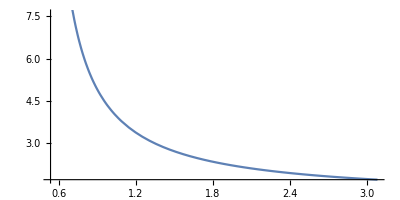

```mathematica
GraphicsGrid[{{
Plot[{r10, r21},{w,1,1.16}, PlotLegends->Placed[{"χ2/χ1",""},Above]],
ParametricPlot[{r10, r21},{w,1,1.16}, AspectRatio->1/2]
}}]
```

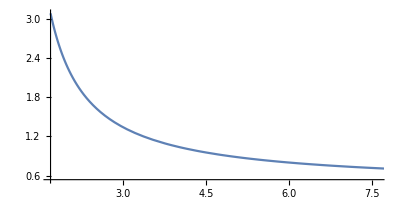

```mathematica
ParametricPlot[{r21, r10},{w,1,1.16}, AspectRatio->1/2]
```

## Numerical values

```mathematica
Xi0 =0.5; Xi1=0.5; Xi2=0.5;
```

```mathematica
Clear[Xi0, Xi1, Xi2];
```

```mathematica
gammaTot = (6.6*10^-22 10^-3)/(0.5*10^-12);
```

```mathematica
Clear[getMcc];
getMcc[out_]:=Switch[out,"chi_c0", 3414.71MeV,"chi_c1", 3510.67MeV,"chi_c2", 3556.17MeV]
```

```mathematica
Clear[Ngamma];
Ngamma[out_, outL_,{Xi0_, Xi1_, Xi2_}]:=Module[{
$Mcc=getMcc[out],
$q2=Switch[outL,"P", mPi, "V", mV, "W",q2]
},
gamma[out, outL]//.{
beta -> √(1-((Mcc+√q2)/MBc)^2)√(1-((Mcc-√q2)/MBc)^2),
GF->1.16*10^-5 GeV^-2,fP->130MeV,fV->140MeV,
Vuq ->0.973,Vbc-> 40.8*10^-3,a1 ->1.14,
Xi[_]->Xi0+Xi1(w-1)+Xi2(w-1)^2
}/.wRule//.{MBc -> 6274.47MeV, mPi->140MeV, mV->770MeV, Mcc->$Mcc, q2->$q2}]
```

```mathematica
<<MyPackages`Histogram`
```

```mathematica
xiList={};
iMax = 10^4;
PrintTemporary[Dynamic[1.i/iMax]];
dfBR = Table[
xis=RandomReal[{-1,1}, 3];
br = 10^5/gammaTot Ngamma[out, "P",xis];
{br, xis}
,{i, iMax}];
```

```mathematica
goodBR = Select[dfBR, 2.4-0.8≤#⟦1⟧≤2.4+0.9&];
```

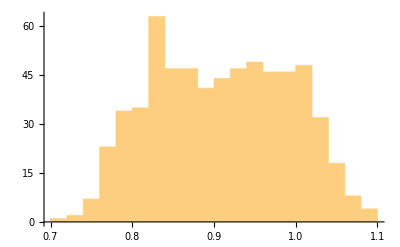

```mathematica
T20P=(Ngamma["chi_c2","V",#]/Ngamma["chi_c2","P",#])&/@goodBR⟦All,2⟧;
Histogram[%]
```

```mathematica
xis = goodBR⟦1,2⟧;
Clear[tabBr, brMN];
Do[
ff = Ngamma[out,"W",{0.5, 0,0}]/.{rhoT[_]->1/(6 π^2), rhoL[_]->0};
tabBr[out] = Table[{q2,100/gammaTot ff},{q2,0,(6.25-getMcc[out])^2, 0.1}];
ListPlot[tabBr[out], Joined->True, AxesLabel->{"q2, GeV^2", "ⅆBr/ⅆq2, 10^-2/GeV^2"}];
brMN[out]=NIntegrate[100ff,{q2,0,(6.25-getMcc[out])^2}]/gammaTot;
,{out,{"chi_c0","chi_c1","chi_c2"}}];
```

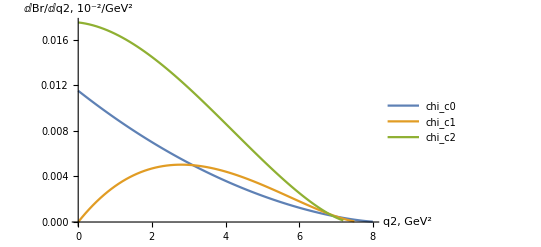

```mathematica
ListPlot[{tabBr["chi_c0"], tabBr["chi_c1"], tabBr["chi_c2"]}, Joined->True, AxesLabel->{"q2, GeV^2", "ⅆBr/ⅆq2, 10^-2/GeV^2"}, PlotLegends->{"chi_c0","chi_c1","chi_c2"}]
```

```mathematica
?UnitStep
```